# WaveletWare Package

Overviewpaclet:WaveletWare/tutorial/WaveletWare Package#311706299 | Quick Startpaclet:WaveletWare/tutorial/WaveletWare Package#16562595

## Overview

(top)

The WaveletWare package is a set of routines that supplement the ideas and applications in the texts

-Graphics-

Discrete Wavelet Transformations: An Elementary Approach with Applicationshttp://www.wiley.com/WileyCDA/WileyTitle/productCd-047018311X.html 
by Patrick Van Fleet (Wiley, 2008)

and

-Graphics-

Wavelet Theory: An Elementary Approach with Applicationshttp://www.wiley.com/WileyCDA/WileyTitle/productCd-0470388404.html 
by David Ruch and Patrick Van Fleet (Wiley, 2009).

The author of the WaveletWare package is Patrick Van Fleethttp://personal.stthomas.edu/pjvanfleet.

The WaveletWare package is the next iteration of the DiscreteWavelets package.  The DiscreteWavelets package was written as a supplement of the text Discrete Wavelet Transformations: An Elementary Approach with Applicationshttp://www.wiley.com/WileyCDA/WileyTitle/productCd-047018311X.html by Patrick Van Fleet.

The WaveletWare package contains several (bi)orthgonal filters and functions that can compute an orthogonal, biorthogonal or wavelet packet transform of a vector, matrix or list of three matrices each of the same dimension.  Several vizualization routines are included as well.

The WaveletWare package also contains routines for image processing, signal/image denoising and the approximation of continuous scaling, wavelet and wavelet packet functions.

### Reference Guides

For reference, the WaveletWare package contains three guides:

1) WaveletWare Overview
2) List of Functions - Alphabetical
3) List of Functions - Categorical
4) List of Options and Values
Several tutorials are included with the package.  See the list at the bottom of this page under Related Tutorials.  In particular, the tutorial Differences in the DiscreteWavelets and WaveletWare Packages describes changes, enhancements, and additions in moving from the DiscreteWavelets package to the WaveletWare package.

This loads the package:

```mathematica
<<WaveletWare`
```

## Quick Start

(top)

### Filters

(top of section)

Here are some filters from the WaveletWare package:

```mathematica
Haar[] 
Daub[4]
Daub[6]
SplineFilters[2,2]
CDF97[]
```

{1/(√2),1/(√2)}

{0.48296291314453,0.83651630373781,0.22414386804201,-0.12940952255126}

{0.3326705529501,0.8068915093111,0.4598775021185,-0.13501102001,-0.08544127388203,0.03522629188571}

{{-1/(4 √2),1/(2 √2),3/(2 √2),1/(2 √2),-1/(4 √2)},{1/(2 √2),1/(√2),1/(2 √2)}}

{{0.0378285,-0.0238495,-0.110624,0.377403,0.852699,0.377403,-0.110624,-0.0238495,0.0378285},{-0.0645389,-0.0406894,0.418092,0.788486,0.418092,-0.0406894,-0.0645389}}

### Computing and Plotting Wavelet Transformations

(top of section)

In the cell below, an image is loaded and its wavelet transformation is computed and plotted.

```mathematica
file=PackageDirectory[DataType->Images]<>"dog.png";
A=ImageRead[file,Resize->{256,384}];
ImagePlot[A]

wt=WT[A,Daub[4],NumIterations->3];
WaveletPlot[wt,NumIterations->3]
```

-Graphics-

-Graphics-

### Wavelet Packet Transformations

(top of section)

Load an image and compute and plot its wavelet packet transformation.

```mathematica
file=PackageDirectory[DataType->Images]<>"benches.png";
A=ImageRead[file];
ImagePlot[A]

{wt,tree}=WPT[A,SplineFilters[2,2],NumIterations->3,CostFunction->NumberAboveThreshold,SecondParameter->35];
ShowBestBasis[tree,Show3D->False]
WaveletPlot[wt,tree]
```

-Graphics-

-Graphics-

-Graphics-

### Image Processing

(top of section)

The cell below illustrates some different image processing tools available in the package.

```mathematica
file=PackageDirectory[DataType->Images]<>"pigeon.png";
A=ImageRead[file,Resize->{256,384}];
ImagePlot[A]

B=GammaCorrection[A,.5];
ImagePlot[B]

B=HistogramEQ[A];
ImagePlot[B]
```

-Graphics-

-Graphics-

-Graphics-

Color images can be converted to different color spaces.

```mathematica
file=PackageDirectory[DataType->Images]<>"goats.png";
A=ImageRead[file,Resize->{256,384}];
ImagePlot[A]
ImagePlot[A,ChannelColor->{Red,Green,Blue}]

YCbCr=RGBToYCbCr[A,DisplayMode->True];
ImagePlot[YCbCr,PlotTogether->False]

HSI=RGBToHSI[A,DisplayMode->True];
ImagePlot[HSI,PlotTogether->False]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

Huffman codes can be computed and visualized.

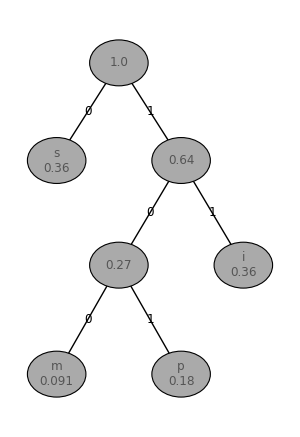

```mathematica
text="mississippi";
{codes,old,new}=MakeHuffmanCodes[text];
HuffmanTree[codes,ImageSize->300]
```

### Approximating Scaling and Wavelet Functions

(top of section)

The Cascade Algorithm is programmed into the package and can be used to approximate scaling and wavelet functions.

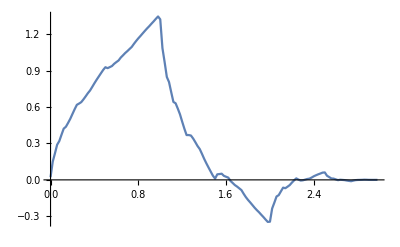

```mathematica
data=ScalingFunctionData[Daub[4]];
ListPlot[data,Joined->True,PlotRange->All,ImageSize->400]

t=Map[WaveletFunctionData[Daub[4],NumIterations->#]&,Range[0,6]];
(* Click the mouse on the second image to see all iterations *)
FlipView[Map[ListPlot[#,Joined->True,PlotRange->All,ImageSize->400]&,t]]
```

### Denoising

(top of section)

Sample a function, add noise and then use wavelet methods to remove the noise.

```mathematica
g[t_]:=4Sin[4Pi*t]-Sign[t-.3]-Sign[.72-t];
{sigma,n}={.35,1000};
original=g[Range[0,1-1/n,1/n]];
ListPlot[original,Ticks->{Range[0,n,n/4],Range[-4,4,2]},PlotLabel->"Original Signal"]

y=original+WhiteNoise[n,sigma];
ListPlot[y,Ticks->{Range[0,n,n/4],Range[-4,4,2]},PlotLabel->"Noisy Signal"]

newy=VisuShrink[y,Daub[4],NumIterations->3];
ListPlot[newy,Ticks->{Range[0,n,n/4],Range[-4,4,2]},PlotLabel->"Denoised Signal"]
```

-Graphics-

-Graphics-

-Graphics-

Related Tutorials

Computing and Plotting Wavelet Packet Transformations

Computing and Plotting Wavelet Transformations

Data Structures in the WaveletWare Package

Differences in the DiscreteWavelets and WaveletWare Package

Managing Multimedia Files in the WaveletWare Package

Naive Image Compression and Edge Detection